# Projectile Motion

```mathematica
params = {θ->π/4, v0->100, g->9.8};
```

```mathematica
eqts = {v0 t Cos[θ],v0 t Sin[θ] - 1/2 g t^2}/.params;
```

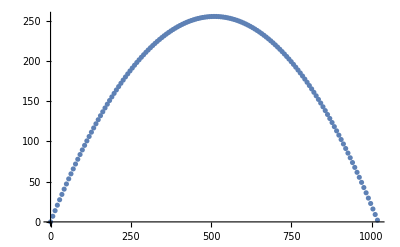

```mathematica
points=Table[eqts,{t,0,14.4,0.1}];
ListPlot[points]
```

```mathematica
points[[2]]
```

{7.07107,7.02207}

```mathematica
Manipulate[Show[Graphics[{White,Rectangle[{-10,-10},{1050,300}]}],Graphics[{Blue,Disk[Evaluate[points[[i]]],10]}]],{{i,1,"Time"},1,Length[points], 1}]
```